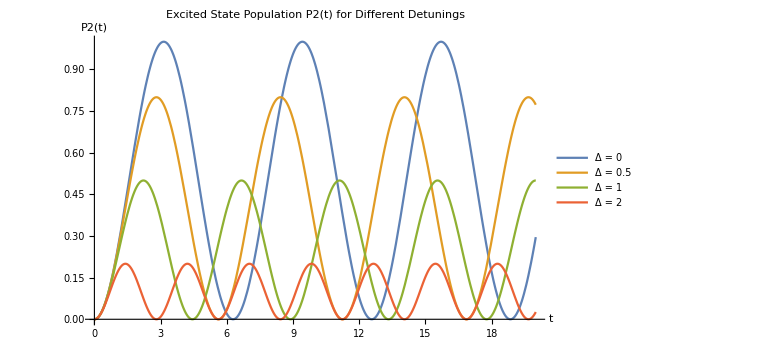

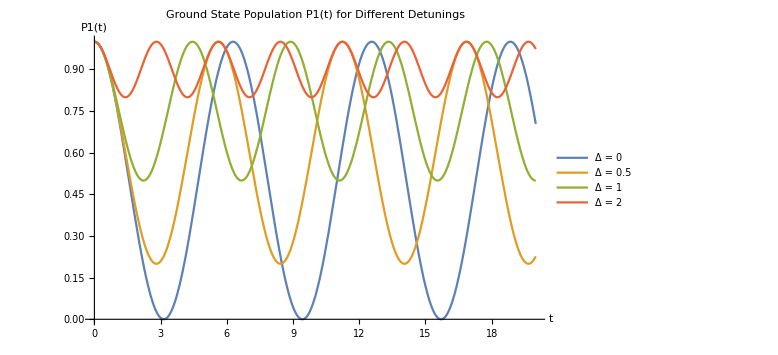

```mathematica
(*Rabi oscillations with detuning:P1(t),P2(t)*)ClearAll[t,Ω,Δ,ΩR,P2,P1];

(*Generalized Rabi frequency*)
ΩR[Ω_,Δ_]:=Sqrt[Ω^2+Δ^2];

(*Populations*)
P2[t_,Ω_,Δ_]:=(Ω^2/ΩR[Ω,Δ]^2)*Sin[(ΩR[Ω,Δ] t)/2]^2;
P1[t_,Ω_,Δ_]:=1-P2[t,Ω,Δ];

Ω0=1;

(*Detuning values to compare*)
detunings={0,0.5 Ω0,1 Ω0,2 Ω0};

(*Plot P2(t) for different detunings*)
Plot[Evaluate@Table[P2[t,Ω0,Δ0],{Δ0,detunings}],{t,0,20},PlotRange->{0,1},AxesLabel->{"t","P2(t)"},PlotLegends->Table["Δ = "<>ToString[Δ0],{Δ0,detunings}],PlotLabel->"Excited State Population P2(t) for Different Detunings",ImageSize->Large]

(*Plot P1(t) for different detunings*)
Plot[Evaluate@Table[P1[t,Ω0,Δ0],{Δ0,detunings}],{t,0,20},PlotRange->{0,1},AxesLabel->{"t","P1(t)"},PlotLegends->Table["Δ = "<>ToString[Δ0],{Δ0,detunings}],PlotLabel->"Ground State Population P1(t) for Different Detunings",ImageSize->Large]
```